```mathematica
Today
```

Sat 21 Apr 2018

# Solving all lab exercises of an Introductory Java course with Mathematica

Ilkka Kokkarinen, ilkka.kokkarinen@gmail.com

Introduction

The author has taught an introductory Java course CCPS 109 Computer Science I at the Ryerson Chang School continuously for the past sixteen years, basically developing all his own material along the way. Over this time span, the Java language itself has evolved tremendously, from the introduction of generics in Java 5 to the move towards more functional programming spirit with techniques such as computation streams and lambdas in Java 8. As this course nears the end of its lifetime, as the department has chosen to follow the universal trend of switching the introductory programming course to Python, a move enthusiastically 100% endorsed by this author, it is time to take this idea one step further. This document was inspired from the question of how difficult it would be to solve the instructor’s current set of ten weekly labs, each lab consisting of four method writing problems, using Mathematica instead of Java. Along the way, we see what these exercises, originally designed to teach the imperative programming thinking of Java to rank beginners, can teach us about the fundamental similarities and differences between these two languages.
Over these sixteen years, these weekly labs and their exercises also evolved significantly. Usually after each semester, some poorly performing and uninteresting lab problem was replaced by some sparkly new problem. Over time, most of the lab problems eventually fell on the wayside, and of course, a couple of lofty ideas with high hopes turned out to be utter failures with students and were quickly replaced by something that turned out to work better in practice. Pretty much all the remaining problems that have survived this gauntlet of unnatural selection really do have some important and educational point in them that justifies their existence. None of the problems is there as some make-work drudgery to fill that week’s mandatory work quota.
The target audience of this document is mainly intended to be motivated students of all ages who have taken the first year or two of computer science so that they know the basics of imperative programming and the object oriented thinking and style, and who are curious about functional programming languages and their different, often more concise style of thinking and problem solving. Many students gain such motivation after taking the author’s second course of programming where they get to try their hands on Java 8 computation streams to learn what a handy way they are to solve many problems in a way that is completely different from the usual way of solving problems with loops. (Streams also have the additional advantage of being naturally parallelizable without any extra effort from the part of the programmer, leading to an interesting class dicussion in the second programming course about that topic and other advantages of expressing computations in functional style.)
Traditionally, the imperative and functional programming languages have been taught to form a strict duality of opposites that shall never meet. But surely it would be more accurate to say that these paradigms form a continuum on which almost all programming languages then fall depending on to what extent they allow functions and code to be treated and manipulated as first-class citizens of that language. Since the Nineties, languages from both the C family tree and the scripting language paradigm have steadfastly inched towards the functional programming end of this continuum, not trying to reach all the way to the very end but aiming towards that unknown sweet spot that would be the perfect compromise of clarity and power for working programmers to solve actual problems. The examples implemented in this document teach such people how to take the ideas that they would normally implement with loops and mutable arrays, and express these same ideas in functional programming form.
For this level of beginning programmer, the material that teaches functional programming available online is rather lacking, compared to the torrent of material readily available for every imperative and object oriented programming language. Most of such material is just far too simplistic so that it does not explain how to actually do anything using a functional programming approach. The other  alternative is that the material is way too high level so that you would basically need to already be a computer science Ph.D. to even begin to read it, written for people who write compilers and interpreters for fun and who do their thinking in category theory while juggling monads the way us boring normos write loops and conditions. This document aims to fill in this gap with at least a little bit of, if you pardon the pun, concrete. Solving these 42 problems will give the reader a grand tour of pretty much all of the important functions and techniques that make up the Mathematica core language, so this document works as a practical introduction to Mathematica.
The secondary audience of this article are other computer science instructors looking for inspiration for lab exercises either in the imperative or functional programming spirit, or who would just simply enjoy an “over the shoulder” read about the overall thought process that goes into the design of an introductory programming course and its individual labs.

Lab One: Classes and objects
The most fundamental difference between Java and Mathematica is the forced program structure of classes and methods of the former, versus the functional and pattern matching programming style of the latter. This first lab of the Java course, intended to familiarize the student with the concepts of classes and objects (no main method is needed at this point, because the course uses the BlueJ environment that allows Java classes and objects to be manipulated with an interactive graphical GUI to try them out), asks the student to define a simple Rectangle class whose instances have an individual width and height, from which the derived virtual properties of area and perimeter can then be computed.
Mathematica already contains all our familiar and unfamiliar geometric shapes as first class citizens of the symbolics language, so that  the mathematical pattern matching engine can compute their arbitrary properties and transformations. But let us ignore those for the moment, and solve this problem using the basic pattern matching operations of Mathematica. Since everything in Mathematica is an expression for which we can define arbitrary transformation rules of our own choosing, a rectangle can be encoded as an expression of the form rectangle(width, height) for which we define appropriate substitution rules. Of course, “rectangle”, “width” and “height” are just names that mean nothing to the computer. But when naming things, it is important to give them names that ring the correct bell inside the human reader’s brain and allow him to make reasonable inferences based on the semantic associations of those names. (On the other hand, we should not fall into the famous fallacy of artificial intelligence and hallucinate that our chosen names themselves have magical properties that somehow have the power to affect the operation of that program, so that a program that encodes a triple (is, love, emotion) would be somehow different from an identical program that encodes a triple (x98, fooπbar, QQQ). Any program will still work exactly the same after you consistently renamed all its identifiers throughout that program.)

```mathematica
width[rectangle[w_,h_]] := w;
height[rectangle[w_,h_]] := h;
area[rectangle[w_,h_]] := w * h;
perimeter[rectangle[w_,h_]] := 2(w + h);
flip[rectangle[w_,h_]] := rectangle[h,w];
```

These five definitions provide the functionality required in the first lab. Each of the ten labs of the course comes with a JUnit tester class that separately tests each of the four methods required in that lab. To guarantee the appropriate test coverage, the tester for each method generates a large number of random inputs that are individually given to the method currently under testing, and calculates the Adler-32 checksum of the answers returned by the method implementation. (Using some cryptographically stronger but slower checksum would be pointless, since any student able to crack the current scheme would still get off easier simply by honestly writing the specified methods as asked.) This checksum is then compared to the checksum that was produced by the instructor’s private model solution, hardcoded inside the JUnit tester. If these two checksums agree, the student gets the green checkmark in the BlueJ tester interface and 0.5 marks added towards his or her total course grade, these ten labs together accounting for 20 marks of the total course grade of 100.
The Java language guarantees that all possible computations done using the four primitive integer types byte, short, int and long will yield the exact same results in all environments. Since the Java standard random number generator class java.util.Random is also similarly guaranteed to always and everywhere produce the exact same random number stream from the same fixed seed that is hardcoded in the JUnit testers, this approach of testing student code submissions makes reaching good test coverage quite easy for instructors. This scheme works better also for the students who, while working on the lab problems usually at home at whatever time of the week is convenient for them, especially in the case of adult students who have actual real lives and corresponding adult life responsibilities rather than the wandervogel freedom to slouch your behind into the computer lab (which, not unlike the Java language itself, are just another silly relic from a simpler and poorer time when computing power was not as cheap and ubiquitous as it is today) every Friday night, instantly knowing if their method works or not by one mouse click of the green JUnit tester class. Since each lab solution is submitted as a complete BlueJ project folder that includes that JUnit tester, the instructor can also verify and grade the submission in literally ten seconds flat with just a couple of mouse clicks, instead of having to pore through the code and reason whether some particularly novel construction that is different from the instructor’s own model solution would produce some off-by-one error in some corner case. This is why we have machines in the first place, to do this tedious work for us. 
One big downside of this randomized testing is that this process cannot tell the student which particular test cases and how many of them the code failed. The CodingBat interactive Java training website, also used in this course to drill in the Java syntax and thinking, is much better in this sense that its submission process makes the particular failed tests explicit to help the student reason about the exact nature of the bug in his code. This can be ameliorated slightly by having the tester to also compute additional information about the answers returned method, such as the total number of true answers over the test cases when testing some classifier method. If this number differs from the expected result, the fact of whether this count is too high (false positives) or too low (false negatives) guides the student in reasoning and finding the bug. However, in place of a larger programming project, the instructor prefers to serve his students CodingBat for breakfast, lunch and dinner, to really drill in the language syntax and the process of solving problems with the language.
In Mathematica, the same way as in symbolic mathematics in general, we are content to observe that our definitions are mathematically correct. We can still quickly try them out by hand as a simple sanity check, of course.

```mathematica
{height[flip[rectangle[3,6]]],area[rectangle[4, 5]],perimeter[rectangle[10,20]]}
```

{3,20,60}

We can also define pattern matching rules for decisions that were not part of this first lab, since the Java if-else statement has not been taught at this point of the course.

```mathematica
isSquare[rectangle[x_,x_]] := True;
isSquare[_] := False;

{isSquare[rectangle[4,4]], isSquare[rectangle[3,8]]}
```

{True,False}

In Mathematica, all geometric shapes are first class citizens of the entire language same way as all other mathematical objects, with arbitrary symbolic computations and transformation being possible for them. In a formalism where pretty much everything is an expression that consists of a head and some number of arguments, pattern matching rules and other transformations can be liberally applied to everything, and the front end will then render the resulting expressions with a particular head in some more human friendly visual form. Expressions whose head is Graphics are rendered as the graphical shapes that they symbolically represent. But despite how fancy some result looks when rendered on screen, everything is still internally an expression tree, as can always be revealed by applying either function FullForm or TreeForm to any expression to reveal the bare bones of this underlying reality.

{4,π,π/4,5/48 (-16+15 π)}

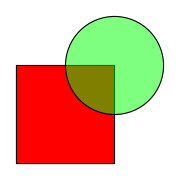

```mathematica
s1 =Rectangle[{0,0},{2,2}];
s2 = Disk[{2,2},1];
s3 = RegionIntersection[s1, s2];
ClearAll[x,y];
{Area[s1], Area[s2], Area[s3], Integrate[x^2+y, {x,y} ∈ s3]}
Graphics[{EdgeForm[{Thick, Black}],Red, s1, Opacity[.5],Green, s2}, ImageSize -> Small]
```

The previous example uses x and y as symbols that are assumed to be uninitialized when used inside Integrate. Whenever symbols are used this way, it is a good idea to use ClearAll to ensure that their names don’t have any values associated with them but remain as pure symbols. This avoids tricky bugs that can easily occur especially if several Mathematica documents are simultaneously open using the same computation kernel. If evaluating another document assigns some values to these symbols, these values get silently substituted in their place inside Integrate, causing the entire computation to do something very different than was originally intended.

Lab Two: Conditions
The second lab of this introductory Java course teaches the students to use the basic if-else conditions to solve decision problems. Nearly every adult is familiar with the ordinary 52 playing cards and how their combinations create virtually infinite possibilities for endless variety of play, which makes playing cards an immediately familiar problem domain for the students to practice programming in both this and the following week's labs. (As Mark Twain noted back in his day, every educated person should at least know that a flush beats a straight.) The four  methods required this week each receive a hand of playing cards as arguments, from which these methods then have to determine whether that hand of cards satisfies the given interesting property such as being a poker flush or a four-of-a-kind. Given a poker hand known to contain exactly five cards, these conditions can be written without any loops, since those have not yet been taught at this point in the course, merely by looking at the five cards and the pairs that they form one at the time inside an if-else ladder. However, the stealthy idea between the lines in all of this week’s problems is preparing the student for the need for loops in the future labs where the string can contain any number of cards, or for that matter, anything at all.
At this point of the Java course, the students have not yet seen arrays, but the previous lecture that covered all the basic data types and their properties and operations has familiarized them with the String class with its basic operations charAt, length and substring, from which all other String operations could in principle be built from ground up. In Mathematica, lists are naturally taught from day one, so in a programming course that uses Mathematica, the five card poker hand would be given as a list of cards. The fully symbolic nature of the Mathematica language would even allow us to represent ranks and suits directly as these symbols, using the Unicode symbols within the language itself to denote the suits.

```mathematica
suitChars = FromCharacterCode[Map[FromDigits[#,16]&,{"2663","2666", "2660", "2665"  }]]
```

♣♦♠♥

However, we can use this opportunity to solve these problems with Mathematica string processing techniques, so that following the specification of the original Java lab, the arguments given to these functions are text strings where each card is encoded as two characters. The first character represents the rank from 23456789TJQKA, followed by the second character representing the suit from cdhs. A hand that consists of n playing cards will then be encoded as a string of precisely the length 2n, with no separator characters inserted between the cards.
The very first lab problem within the previous setup asks for a method that takes the rank given as a character and converts it to its nominal integer value. For simplicity, and following the lightweight spirit of the design by contract software engineering philosophy, in all the labs in the course the method implementations may assume that their argument values are legal as promised in the method specification. These methods therefore don’t need to perform any error detection, let alone error recovery that would be a topic better left for a more advanced course. (The author’s second course of programming, of course, covers the concept of method pre- and postconditions and how exceptions are used to terminate a method that can only throw its hands up in the air in frustration and give up as soon as it realizes that it has been asked to do something that was logically impossible to begin with.)

```mathematica
ranks = {"2","3","4","5","6","7","8","9","T","J","Q","K","A"};
numericalRank[r_] := First[First[1 + Position[ranks, r]]];
Map[numericalRank, ranks]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14}

Given a five-card poker hand encoded as a string of ten characters, the second lab problem of this week asks the method to determine whether that hand is a flush, that is, all of its five cards are of the same suit. In Java, this becomes a straightforward conjunction of equality comparisons between the five suit characters extracted from the hand. The students will hopefully realize at this point that only four equality comparisons suffice, since it is necessary to compare each suit character only to the suit of the first card, due to the transitivity of equality.
In Mathematica, determining whether the hand is a flush can be achieved in a more abstract manner by checking whether the string matches the pattern whose characters on the odd positions we don’t care about, whereas all five characters in the even positions must be the exact same character, whichever suit character that one might be. One very important difference between Java and Mathematica also illustrated in this problem is that Java uses the programmer-style zero-based indexing throughout, whereas Mathematica consistently uses normal people style one-based indexing throughout. (The zeroth index of a list or an arbitrary expression gives the head of that expression, which can cause weird results for somebody who, due to an ingrained habit, accidentally uses zero-based indexing with Mathematica.) We can write this function to work with hands on any length n by building the pattern used for string matching to consist of n separate pieces that are combined together with Nest.

```mathematica
isFlush[hand_] := With[{n = Ceiling[StringLength[hand]/2]},
With[{pat = Nest[(# ~~ _ ~~ suitInFlush_)&,StartOfString, n]},
StringMatchQ[hand, pat]]];
SetAttributes[isFlush, Listable];
isFlush[{"Kh7h2hTh3h", "Qh7s2hTh3h", "7hAh4h"}]
```

{True,False,True}

To test out this function, we can use Table to generate the list of all 52 playing cards, for which basic combinatorics will generate all possible hands of given length. It is more efficient to Subsets instead of Permutations to ensure that every possible hand is produced in exactly one sorted permutation where the cards appear in the same order as they appear in the original deck. The following series of statements then tells us that, ignoring the order in which the cards are in the hand, there are exactly 5148 ways to choose five different cards so that all five have the same suit. However, 40 of these single-suited hands are actually straight flushes. (Precisely forty, because a straight is identified by its lowest card that can be from 1 to 10, ace here serving as a one in the bicycle straight, and each straight flush can then be made from any one of the four possible suits.) Recognizing a straight would be a pretty difficult problem at this point of the course, especially when an ace can be counted as either 1 or 14,  so we simply ignore straight flushes for the purposes of this problem.

```mathematica
suits = {"s","h","d","c"};
deck = Flatten[Table[r <> s, {s, suits}, {r, ranks}]];
flushes = Select[Map[StringJoin,Subsets[deck, {5}]], isFlush];
Length[flushes]
```

5148

The next question asks the student to write a similar method to recognize a poker hand that is a four of a kind. This one, like many other problems, is actually a special case of a more general problem of computing the general shape of the hand when suits are ignored and we only look at the multiset of ranks. Comparing the rank of every card to the ranks of the cards that are placed after it within the hand, and counting how many such internal pairs of cards have equal ranks, gives an integer result whose value directly identifies the poker hand as high card (0), one pair (1), two pair (2), three of a kind (3), full house (4) or four of a kind (6). To go above an beyond the original Java lab problem, we can in fact easily generate all possible five card poker hands, with each permutation of cards produced exactly once, and count how many of these hands are of each type of shape.

```mathematica
internalPairCount[hand_] := With[{rc = Characters[hand]},
Length[Cases[Subsets[ Table[rc[[i]], {i, 1, Length[rc], 2}], {2}], {rank_,rank_}]]
];
shapeConvert[0] := "no pair";
shapeConvert[1] := "one pair";
shapeConvert[2] := "two pair";
shapeConvert[3] := "three of a kind";
shapeConvert[4] := "full house";
shapeConvert[5] := "impossible";
shapeConvert[6] := "four of a kind";
pairCounts = Map[internalPairCount,Map[StringJoin, Subsets[deck, {5}]]];Table[shapeConvert[k] -> Count[pairCounts, k], {k , 0, 6}]
```

{no pair→1317888,one pair→1098240,two pair→123552,three of a kind→54912,full house→3744,impossible→0,four of a kind→624}

These computed counts agree with the Wikipedia page “List of Poker Hands” that say that among all possible five card poker hands, there exist precisely 1,098,240 one pair hands, 123,552 two pair hands, 54,912 three-of-a-kind hands, 3,744 full houses and 624 four-of-a-kind hands. (Derivations of all these counts are elementary exercises for an introductory course on combinatorics.) The remaining 1,317,888 hands that contain no internal pairs then either are lowly high card hands, or they are straights, flushes or straight flushes, none of which can contain any pairs.
As you can also see from the produced list, a five card poker hand cannot contain five internal pairs. The reader can, just for fun, try to create a five-card poker hand with an internal pair count of five to see why this task is logically impossible. This magic number five could be realized in the poker variation of seven card stud, where it would indicate a shape that contains one three of a kind, one pair and then another pair. Such deceptively nice-looking hand is a bit disappointing due to its redundancy in power, because the extra pair does not elevate this hand any higher in the poker hand rankings.
The fourth, and thus the final, question of this second lab asks for a method that can identify whether the given hand of cards is a badugi from the exotic poker variation of the same name, that is, its no two cards are of the same rank or the same suit. Quick combinatorial counting with our fingers reveals that there is a total of 3 + 2 + 1 = 6 comparisons to be made between the six internal pairs, and the cards within each internal pair must be separately compared with for equality by suit and by rank. Restricted to hands of four cards, this method therefore needs to perform exactly 12 equality comparisons, unless the student has peeked a couple of weeks ahead in the material to be able to simplify this logic with nested loops. This problem also indirectly teaches the students the very important de Morgan’s laws of negating logical expressions, as soon as their first attempt of essentially negating the logic of flush identification method mysteriously fails to produce the correct answers that would pass the JUnit testers.
Since there exist only four possible suits, a hand can have at most four cards and still qualify as a badugi. Since this method once again does not need to be prepared for illegal arguments, it can be solved as a one-liner by extracting all its characters into a list and then removing the duplicate elements using Union. If this operation does not shorten the length of the list, that means that there were no duplicated ranks or suits anywhere in that hand begin with, and that hand is therefore a badugi.

```mathematica
isBadugi[hand_] := Length[Union[Characters[hand]]] == StringLength[hand];
```

If we may again take a little sidebar into introductory combinatorics, the number of different k-card badugis can be computed easily by realizing that each badugi is simply some way to choose k different ranks out of 13 possible ranks. These k cards then also each must be of a different suit, but we can choose those k suits freely from the four possible suits, and assign our chosen suits to go with the chosen k ranks using an arbitrary permutation from the k! possibilities.

```mathematica
badugis = Table[Length[Select[Map[StringJoin,Subsets[deck, {k}]], isBadugi]],{k,1,4}]
expected = Table[Binomial[4,k] *k!* Binomial[13, k],{k,1,4}]
```

{52,936,6864,17160}

{52,936,6864,17160}

Alternatively, we could have used Mathematica’s powerful string pattern matching engine to determine whether the given hand is a badugi. Having done so below as a one-liner using string pattern matching that looks for any character that is repeated, we can quickly verify that both functions return the same answer for all possible sorted hands of four or fewer cards.

```mathematica
isBadugiS[hand_] := Not[StringMatchQ[hand, ___ ~~ x_ ~~ ___ ~~ x_ ~~ ___]];
And @@ Table[isBadugi[hand] == isBadugiS[hand], {hand, Map[StringJoin,Subsets[deck, 4]]}]
```

True

## Lab Three: Loops

The third lab of this introductory Java course continues on the previous week’s theme of hands made up of playing cards that are encoded as strings of two characters, one for the rank and one for the suit. However, in this week’s lab the hands are too long for even the most careful student to encapsulate the entire logic into a giant if-else ladder of individual card comparisons, so some sort of loop must necessarily be used to solve each problem.
The first question moves from the seedy and smoke-filled back rooms of poker to the more raffinated air of contract bridge where each player is dealt a hand of thirteen cards, a little bit too many to handle without any loops. The Milton Work point count, the rudimentary (but surprisingly effective when compared to its almost silly simplicity) hand evaluation scheme that every beginning bridge player learns during the first couple of introductory bridge lessons, assigns each ace a work point value of 4, each king a work point value of 3, each queen a work point value of 2, and each jack a work point value of 1. Nothing else matters, although some people also count the tens as half points. The shape of the hand otherwise does not matter for this point count, since a beginning player could not reason anything about the playing potential of the hand based on its the shape anyway, especially when this reasoning has to be executed in the context of the current bidding so far. The first question of this week’s lab asks the student to write a method to compute the work point count of the given bridge hand.

```mathematica
pointValue["A"] := 4;
pointValue["K"] := 3;
pointValue["Q"] := 2;
pointValue["J"] := 1;
pointValue[r_ /; StringLength[r] == 1] := 0;
pointValue[hand_ /; StringLength[hand] > 1] := Plus @@ Map[pointValue, Characters[hand]];
```

There are a little bit too many thirteen card hands for us to count through them all, but random sampling of 100,000 bridge hands should give us a reasonable estimate of the average point count of a bridge hand, which should naturally be 10, since the fixed 40 work points in the deck are divided over four players. While we are at it, we can also calculate the standard deviation of this distribution of points, and count how often the player is dealt a yarborough, that is, a hand without any aces or faces. (Technically, a proper yarborough does not contain any tens, but they would not affect our simple point count anyway.)

```mathematica
bridgeHand := StringJoin[RandomSample[deck, 13]];
workSamples = Table[pointValue[bridgeHand], {i, 1,100000}];
{N[Mean[workSamples],5],N[StandardDeviation[workSamples],5],N[Count[workSamples, 0] / 100000,5]}
```

{10.005,4.1108,0.00359}

In fact, we can now easily find out from those sample hands what portion of them contain some particular number of work points.

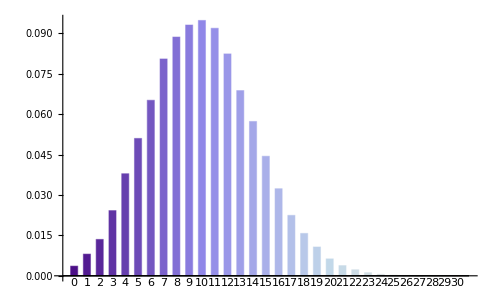

```mathematica
pointDist = Table[N[Count[workSamples, k] / Length[workSamples]], {k, 0, 30}];
BarChart[pointDist,BarSpacing -> 0.8, ChartLabels -> Table[k, {k, 0, 30}], ChartStyle -> "LakeColors"]
```

Question two of this week’s lab asks the player to compute the number of deadwood points in the game of gin rummy for the cards that remain in the hand after all possible discards to melds have been done. This lab also is the first one of many to drive in the idea that in programming, zero is always a possibility that all computations must be prepared for. The general principle that cannot be overemphasized is that whenever there is nothing to do, the only correct thing is to do nothing at all. This whole notion is counterintuitive to most people who are not programmers, since our systems and processes designed for the real world of humans tend to implicitly assume that there is always at least one of something for the operation to make sense to begin with. The author always likes to joke in the class at this point that if any of his students ever goes to a supermarket checkout lane with no groceries, pays zero dollars for the contents of his empty cart and receives a receipt for zero dollars before leaving, get a friend to surreptitiously video this transaction and post it on YouTube.

```mathematica
deadwood[""] := 0;
deadwood["A"] := 1;
deadwood["K"] := 10;
deadwood["Q"] := 10;
deadwood["J"] := 10;
deadwood["T"] := 10;
deadwood[r_ /; StringLength[r] == 1] := If[DigitQ[r], ToExpression[r], 0];
deadwood[hand_ /; StringLength[hand] > 1] := Plus @@ Map[deadwood, Characters[hand]];
```

Question three goes back to the game of contract bridge and asks the student to generate the shape of the hand by listing how many spades, hearts, diamonds and clubs the hand contains, in this order. In the original question, the answer must be given as a string where these counts are separated with commas. However, here in Mathematica we now return the answer as a list, because a list can always be converted to a string if desired using StringJoin, and we wish to next perform another interesting computation on bridge hand shapes that would require a conversion to a list anyway.

```mathematica
handShape[hand_] := Table[StringCount[hand,suit], {suit, suits}];
```

We can now go above and beyond the Java programming lab and estimate the probabilities of getting dealt some particular hand shape patterns where the order of suits does not matter. Sorting the hand shapes before using Gather to create a list of sublists of equal shapes eliminates the suit order. Each sublist of equal shapes is then turned into a rule whose left side is the shape and the right side is the length of that sublist. The estimates computed from 200,000 sample hands are pretty close to those given on the Wikipedia page “Contract Bridge Probabilities”. As is conventional in bridge literature, the overall shape where the order of suits does not matter is denoted by using minus signs to separate the lengths of the suits. The following table shows the shapes ordered by their frequency over 200,000 sample hands. The second column gives the observed count of that shape over 200,000 generated sample hands, whereas the third column displays the exact expected count over that number of hand, the function exactShapeCount derived using some clever combinatorics taken from the web page “How to Calculate Bridge Suit Probabilities” by “Durango Bill”. The fourth column then shows how many daily duplicate tournaments consisting of 26 hands each a bridge enthusiast would have to play on average before he is dealt a hand of the particular shape. As this computed table shows, 6-3-3-1 is the most frequent shape among the shapes that one literally does not expect to see every day.

```mathematica
bridgeSamples = 200000;
exactShapeCount[shape_] := (4! * Times@@Map[Binomial[13,#]& ,shape] / If[MatchQ[shape,{___,x_,___,x_,___}], 2, 1]) / If[MatchQ[shape, {___,x_,___,x_,___,x_,___}], 3,1];
handShapeList =Reverse[SortBy[ Map[({Row[First[#],"-"],Length[#],Round[bridgeSamples*exactShapeCount[First[#]] / Binomial[52,13]], N[1/((Length[#]/bridgeSamples) * 26)]})&,Gather[Table[Reverse[Sort[handShape[bridgeHand]]],{i, 1, bridgeSamples}] ]],(#[[2]])&]];
TableForm[handShapeList,TableHeadings ->{None, {"Shape", "Frequency","Exact", "Daily duplicates needed"}}]
```

Shape | Frequency | Exact | Daily duplicates needed
--4432 | 43204 | 43102 | 0.178046
--5332 | 30849 | 31034 | 0.249354
--5431 | 25889 | 25861 | 0.297126
--4333 | 21232 | 21072 | 0.362298
--5422 | 21049 | 21159 | 0.365448
--6322 | 11389 | 11285 | 0.675416
--6421 | 9286 | 9404 | 0.828377
--6331 | 6785 | 6896 | 1.13372
--5521 | 6366 | 6348 | 1.20834
--4441 | 5981 | 5986 | 1.28612
--7321 | 3794 | 3762 | 2.02749
--6430 | 2725 | 2652 | 2.82287
--5440 | 2512 | 2487 | 3.06222
--5530 | 1779 | 1790 | 4.32395
--6511 | 1332 | 1411 | 5.77501
--6520 | 1297 | 1302 | 5.93085
--7222 | 1056 | 1026 | 7.28438
--7411 | 791 | 784 | 9.72479
--7420 | 741 | 723 | 10.381
--7330 | 500 | 530 | 15.3846
--8221 | 408 | 385 | 18.8537
--8311 | 237 | 235 | 32.457
--7510 | 229 | 217 | 33.5909
--8320 | 214 | 217 | 35.9454
--6610 | 159 | 145 | 48.3793
--8410 | 111 | 90 | 69.3001
--9211 | 30 | 36 | 256.41
--9310 | 18 | 20 | 427.35
--9220 | 16 | 16 | 480.769
--8500 | 10 | 6 | 769.231
--7600 | 6 | 11 | 1282.05
--10210 | 2 | 2 | 3846.15
--9400 | 2 | 2 | 3846.15
--10111 | 1 | 1 | 7692.31

As was pointed out in item 46 of HAKMEM, the decades old collection of old-timey mathematical and programming tricks and general observations, the most probable bridge hand shape is 4-4-3-2 instead of the intuitively more appealing 4-3-3-3, even though the latter shape is more evenly distributed. Also, as most bridge players should soon enough learn, to the first approximation this maximally balanced shape pretty much always plays about two work points worse than it would initially be expected to, an important stepping stone towards the general realization that a whole lot of other things matter hugely for the bridge hand than just the raw work points. The purpose of the bridge hand is to take enough tricks until the opponents take too many, and the work count is just a simple statistical estimate of the average power that may or may not be applicable to the current situation at hand.
Another similarly counterintuitive truth about bridge hand distributions is that an even number of missing cards is more likely to break unevenly into your two opponent’s hand than to break evenly between them. For example, six missing cards are more likely to break 4-2 than 3-3, which makes it often a better move to play for the finesse than the brute force drop. (Dealing out the cards one at the time, the 3-3 distribution can result only from the 3-2 or 2-3 distribution of the previous five cards, and the sixth card is equally likely to end up in either hand, giving both 4-2 and 3-3 distributions an equal probability from these predecessor states. However, the 4-2 final distribution can also additionally emerge from the 4-1 and 1-4 distributions of the first five cards, both of which themselves have a nonzero probability and make the outcome of 3-3 impossible.)
The last question this week goes back to poker, asking for a method that recognizes whether the given five-card poker hand is a full house, that is, contains some three cards of equal rank and another pair of cards of some other rank. Without giving any hints, this question was intentionally intended to be a bit tricky, to force the students work out the necessary conditions and loops from various different possible ways. From the very beginning, the author emphasizes the importance of the idea that since all programming is really just a high level syntactic sugar for the fundamental foundation of propositional logic, it automatically follows from the properties of propositional logic formulas that whenever there is one way to solve some problem, there always exist many other, result-equivalent ways to solve that same problem. But in this document, identifying whether the given hand is a full house was already a special case of identifying the general shape of the hand last week, so we don’t need to repeat its code here.

Lab Four: String operations

Text strings serve as a convenient stepping stone to arrays that will be introduced the week following this one, with the String methods length and charAt readily corresponding to the concepts of the array length and the positional indexing of its elements. The String class in Java also serves as an enormous contrast to the character and other arrays whose primitive and low level nature will surely annoy anybody who has already been spoiled by the power and convenience of, say, strings and lists in Python. Whereas Java strings are jam-packed with powerful methods for frequently needed operations on text (and in case those are somehow not enough to finish the job at hand, the packages java.util.regex and java.text fill in the gaps), the primitive Java arrays offer basically diddly squat for the programmer. Even the methods that all classes must have by law, such as toString and equals, are implemented in a way that makes these methods practically useless. (At least the utility class Arrays ameliorates this defective setup a little bit.)
The fourth lab of this course asks the students to implement various operations on text strings whose length and character structure are unlimited. These methods still require one loop through the string, since in the last question, the String method indexOf to find the first position of the character inside the given string will do the work of an inner loop. The first question asks for a method that creates and returns a new string that is otherwise the same as its argument string, except all of its runs of consecutive characters have been turned into single characters.
The JUnit testers for this week are intentionally written to generate long strings of random character bursts as test cases, so that any solution that builds up the answer by adding immutable strings will end up taking a lot of time to slough through these tests. Of course, the mutable StringBuilder has already been introduced in the lectures covering both the theory of its internal operation and the practice with examples of using that class to build up the answer. This part of the lectures segways to the fun general discussion of how in computing it is often possible to trade space for time and vice versa, but since we have ample memory in our computers these days and time keeps getting more expensive, we will always try to cache previous results instead of recomputing them from scratch.
For the humour value, let us now write some Java using Mathematica, in spirit of the classic programmer observation of how it is possible to write Fortran in any language.

```mathematica
removeDuplicatesJavaStyle[text_] := Module[{chars,result, i},
chars = Characters[text];
result = {};
For[i = 1, i≤ Length[chars], i++,
If[i == 1 ||chars[[i]] ≠ chars[[i-1]],
AppendTo[result, chars[[i]]];
]
];
StringJoin[result]
];
removeDuplicatesJavaStyle["aabbbbbabbbbccccddd"]
```

ababcd

However, many other ways to solve this problem more in the general spirit of Mathematica can surely be thought of. The author has a feeling that he is probably missing the best one in this sense. Here are two suggestions meanwhile.

```mathematica
removeDuplicatesSplit[text_] :=StringJoin[Map[First, Split[Characters[text]]]];
removeDuplicatesFixedPoint[text_] := FixedPoint[StringReplace[#, c_ ~~ c_ :> c]&, text];
Table[f["aabbbbbabbbbccccddd"], {f,{removeDuplicatesSplit,removeDuplicatesFixedPoint}}]
```

{ababcd,ababcd}

The second question asks for a method that splits its argument string into individual words separated by one or more whitespace characters. Of course, a clever student who has, as our friends across the pond would say, taken a butcher’s through the Java API documentation would realize that there already exists a method in String to do precisely this, and there is no harm pointing such out possibility after the lab to remind the students that most wheels that people need to drive have long since been invented over and over, so there is no point for anybody to reinvent them unless they feel they could use more exercise in the art of wheelmaking. But even working from scratch, the student will soon realize that it is necessary to use the utility method Character.isWhitespace to recognize the whitespace characters, since the Unicode character standard defines a whopping 25 different whitespace characters! (In addition to the familiar troika of the ordinary whitespace, tab and newline characters, how many of these other whitespace characters can the reader name?) Since in Mathematica, this whole method would just be one call to StringSplit, we could now at least pretend to do a little bit of extra work and implement this function properly so that it will recognize all these exotic 25 whitespace characters.

```mathematica
unicodeWhitespaces = {9, 10, 11, 12,13, 32, 133, 160, 5760, 8192, 8193, 8194, 8195, 8196, 8197, 8198, 8199, 8200, 8201, 8202, 8232, 8233,8239, 8287, 12288 };
splitWords[text_] := 
Map[FromCharacterCode, 
Select[SplitBy[ToCharacterCode[text], MemberQ[unicodeWhitespaces,#]&], (Not[MemberQ[unicodeWhitespaces,First[#]]])&]
];

splitWords["  Hອllo world! H☺w      are yôu today?"]
splitWords[FromCharacterCode[{97, 160, 98, 5760, 99, 8192,100, 8193, 101, 8194}]]
```

{Hອllo,world!,H☺w,are,yôu,today?}

{a,b,c,d,e}

Just out of curiosity, let’s find out how many Unicode characters from the above list Mathematica actually recognizes as whitespaces. Really, only six?

```mathematica
Map[ToCharacterCode, Select[CharacterRange[FromCharacterCode[1], FromCharacterCode[13000]], StringMatchQ[#,Whitespace]&]]
```

{{9},{10},{11},{12},{13},{32}}

The next question in this lab is our first example of writing a for-loop that maintains some state information along the way that helps it decide what to do for each input character that it processes. The problem asks to convert the argument string to a result of equal length but where the first letter of every word is converted to title case, and all other characters are kept as they were. This second requirement includes all whitespace characters, so we cannot use split here to separate the words, since doing so would lose the distinction between different types of whitespace characters and, more importantly, their counts. On a quick googling of the topic, Mathematica does not seem to make the distinction between title case and upper case, so we are content to convert each character that is preceded by some whitespace character to uppercase.

```mathematica
convertChar[{c1_,c2_}] := If[StringMatchQ[c1, WhitespaceCharacter], ToUpperCase[c2], c2];
convertToTitleCase[text_] :=StringJoin[Map[convertChar,  Partition[Join[{" "}, Characters[text]],2,1]]];
convertToTitleCase["well hello there old chap, how are yeh?"]
```

Well Hello There Old Chap, How Are Yeh?

The last question of this week is similar to the first one, but instead of comparing each character to its immediate predecessor to determine whether that character will become part of the result, this question compares each character to all the previous characters that have been already included in the result. This result will then contain every character that appears in the original text, but each character included exactly once. Furthermore, these characters are required to appear in the result in the exact same order that they first originally appeared in the text, so we can’t just say Union[Characters[text]] to solve this problem as a one-liner. This problem might initially seem like it necessarily needs to be solved in an imperative fashion, maintaining a data structure that remembers the characters that have already been encountered in the previously iterated positions. But the same as with any computation, functional programming operators are Turing-complete and can always be combined in a myriad different ways to produce the result of any computation in a non-imperative fashion. 
The following expression, the most convoluted lab solution that we have seen so far, is easiet to decipher from inside out. Its innermost subexpression first uses MapIndexed, the nifty and crafty generalization of Map that operates on each element and its position instead of only the element itself, to allow it make decisions based on not just the element of the list but its position. This operation converts the list of characters into a list of pairs of the form {c, i} where c is the original character and i is its position in the string. This list of pair is then sorted based on the first component to make all occurrences of the same original character to end up in consecutive positions of the list. The sorted list is split into sublists of equal characters with the function SplitBy so that each sublist contains all consecutive occurrences of that particular character. Since we care only about the first occurrence of each character, we apply Map to these sublists to extract the First occurrence of each character, still in the form of a pair {c, i}, but i is now guaranteed to be the position of the first occurrence of that character. These pairs are then sorted again, but now based on the position i, to effectively return each character in the list in its place in the original order. Finally, the original characters are extracted from these pairs by dropping the now redundant position component, and the resulting list of characters is turned back into a string using StringJoin. (In the classic Lisp functional programming language, this idiom is known as decorate-sort-undecorate.)

```mathematica
uniqueCharacters[text_] := StringJoin[Map[First,SortBy[Map[First, SplitBy[SortBy[MapIndexed[({#1, First[#2]})&, Characters[text]], First], First]], #[[2]]&]]];
uniqueCharacters["Hello there, world! How are you doing in this day of the year 2018?"]
```

Helo thr,wd!ayuingsf2018?

## Lab Five: Arrays

The fifth lab finally leads the students of this introductory Java course to arrays, a topic that at this point should not be all that frightening once they realize that the logic of array operations is exactly same as it was with text strings, just with a teeny bit different syntax for the length and positional indexing operations. From our point of view after all the previous labs, it should not come as a surprise that all four lab questions of this week can be written out as one-liner rules that operate over Mathematica lists.
The first problem of this week asks for a method everyOther that creates a new array that contains all elements in the even-numbered positions of the parameter array. (This problem statement assumes the usual Java zero-based indexing, so rewritten in Mathematica conventions, this question actually asks for the elements in the odd-numbered positions of the list.) The main difficulty with this problem for the tyro is ensuring that the result array has the correct length, since it is easy to be off by one in the result length calculations. At this point, the author likes give my students the same useful piece of advice that he can still somehow remember from his second grade teacher: do your calculation using small numbers first to see if your calculation steps make sense. Counting with fingers to find out how many elements end up in the result usually helps the students find the correct rule, although only very advanced students can turn this particular computation into a one-liner followed by the element copying logic, instead of writing two separate branches of the same copying logic for the odd and even parameter array lengths.
But seeing how the thoroughly modern Mathematica is touted for its advanced machine learning capabilities, let’s have a fun little comparison of which party is smarter, Mathematica or the average student, in the task of determining how many elements the result array will contain. The function Predict that automatically builds a model to best fit its training data is given as this training data a small set of examples of the correct result lengths for the particular lengths of parameter arrays.

```mathematica
trainingSamples = {1-> 1, 2-> 1, 3-> 2, 4-> 2, 5-> 3, 6-> 3, 20-> 10};
evaluatePredictor[p_] :=Count[Table[Round[p[i]] == Floor[i / 2] + Mod[i, 2], {i, 1, 20}], True];
Table[evaluatePredictor[Predict[trainingSamples, Method -> m]], {m, {"LinearRegression", "NeuralNetwork","RandomForest"}}]
```

{19,14,6}

As seems intuitively reasonable, linear regression finds the best fit for a problem that is practically a linear function, although it still misses one of our twenty validation tests. So that is one point for the humans at this point of the future timeline. Alternatively, we can also check how well FindSequenceFunction fares with this same task. Well, it does find something all right, but definitely not the same formal expression that a normal human would find for this problem.

```mathematica
tableLength = FindSequenceFunction[{1,1,2,2,3,3,4,4,5,5,6,6}]
FullSimplify[tableLength, ComplexityFunction -> LeafCount]
Table[tableLength[k],{k,1,20}]
```

1/4 (-1)^#1 (-1+(-1)^#1+2 (-1)^#1 #1)&

1/4 (-1)^#1 (-1+(-1)^#1+2 (-1)^#1 #1)&

{1,1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10,10}

After this fun little digression into this refreshing modern day John Henry tale, the following solution to the original problem uses Partition to split the list into sublists of two elements, from each of which we take the first one and discard the second. By itself this approach would fail for any list of odd length, since the last element would not become part of this partition. Fortunately, the Partition function can be given extra control parameters to handle precisely these sorts of common situations. Even though the original lab problems guaranteed that the method can assume its arguments to conform to the lab specification, we can easily define this rule to match patterns with the particular Head.

```mathematica
everyOther[v_List] := Map[First, Partition[v,2, 2, {1,1}]];
everyOther[Range[20]]
```

{1,3,5,7,9,11,13,15,17,19}

The concept of inversion is important in combinatorics and the theory of sorting algorithms, as a measure of how “out of order” the array elements are compared to the positions that those elements would end up when sorting the array. An n-element array that is already sorted has zero inversions, the minimum possible number, whereas an array that is sorted in reverse order has n(n - 1)/2 inversions, the maximum possible number.
To count the number of inversions of the given array in Java, coincidentally the second question in this week’s lab, done in the brute force way that a student of a first programming course can understand and express in code, requires the use of two nested loops for the first time in this course. The outer loop iterates through the positions of the array, and the inner loop iterates through the positions that come after the current position of the outer loop counter. The rest is just your basic counting problem of initializing an integer counter to zero and incrementing it every time a new inversion is encountered. But this is pretty much the exact opposite to how we would solve this problem properly as a functional programming one-liner in Mathematica. The pattern matching rule to choose the element pairs where the order of element values is opposite to the order of their positions uses a conditional pattern to do this work. The handy function Subsets can be used to generate all element pairs, triples, quartets and so on, to do the work of nested loops of that depth.

```mathematica
countInversions[v_List] :=Length[Cases[Subsets[MapIndexed[({#1, First[#2]})&, v],{2}],{{a_,b_},{c_,d_}} /; a > c && b < d]];
countInversions[{8, 2, 3, -1, 4, 1}]
countInversions[Range[100,1,-1]] == Binomial[100, 2]
```

10

True

The third question of this lab is the first one in these weekly labs to have the return type void. The required method modifies the elements of its argument array, instead of creating an entire new array to contain the result and return that. (At this stage of the course, those students who cannot conceptualize the difference between returning a result and printing that result on the screen seem to have mysteriously vanished.) Since passing a reference by value is for all practical purposes equivalent to passing that object by reference, back in the nineties when Java as pretty much all of life was much simpler than now, people used to have big fights as modern day versions of the “big-endians” and “little-endians” of Gulliver’s Travels about whether that means that Java also has call-by-reference parameter passing mechanism in addition to the usual call-by-value. Such bitter fights over words have long since subsided as our attention span has turned to more pressing matters. But wouldn’t this still be a good time to find out how assignment and parameter passing mechanisms work in Mathematica?

```mathematica
ClearAll[parameterTest];
parameterTest[v_] := Module[{e},
e = v;
e[[2]] = 42;
Print["Inside the function we have ", e[[2]]," ", v[[2]]];
MapAt[(42)&, v, 2]
];
v =Range[100];
parameterTest[v];
Print["Outside the function we have ", v[[2]]];
```

Inside the function we have 42 2

Outside the function we have 2

In proper functional programming thinking, modifying data inside a function is a huge no-no anyway. But now, we still return to the original lab problem of rearranging the array elements so that all nonzero elements are in one bunch in the beginning, followed by all the zero elements in the array. The function must also maintain the original order of these nonzero elements. As always when separating list elements into two groups, either one of the functions Cases and Select, depending on whether the selection criterion happens to be a pattern or a function predicate, will do the job. (The opposite of Cases in the sense in that it keeps the elements that Cases discards and vice versa is named DeleteCases, whereas the negation of Select is named... (drum roll)... Select, the exact same function used with  a logical negation placed in front of the function used as the selection criterion.)

```mathematica
squeezeLeft[v_List] := Join[DeleteCases[v, 0], Cases[v,0]];
squeezeLeft[{42, 1, 0, 0, 7, 0, 99, -2, 0,-99}]
```

{42,1,7,99,-2,-99,0,0,0,0}

Alternatively, the function GatherBy could also do the job here. GatherBy (or simply Gather, if the selection criterion is the element value equality) is more general than Cases and Select in that the elements of the list can be partitioned to any number of equivalence classes, not merely two. The result is a list of lists of the elements of each equivalence class, so flattening this list brings all the elements back to the top level but with equal elements gathered together as a clump. We give Flatten the optional level specification of 1 to ensure that the flattening does not continue recursively to the sublist structures, which would make a difference for the elements that were themselves lists instead of integers.

```mathematica
squeezeLeftGatherBy[v_List] := Flatten[GatherBy[v, (#!= 0)&], 1];
squeezeLeftGatherBy[{42, 1, 0, 0, 7, 0, 99, -2, 0,-99}]
```

{42,1,7,99,-2,-99,0,0,0,0}

The last problem of this fifth week requires the student to create and return a new array whose exact length is not known at the beginning of the method execution, unlike all the other array methods that have been used as examples and lab problems so far. The method that implements run length decoding is given an array whose length is guaranteed to be an even number, so that each pair of consecutive elements (n, v) is expanded into n copies of element v. For example, the array [1000000, 42] would expand into a million element array whose every element has the same value 42. The Java implementation has to first loop through the parameter array and add up every other element working as n, and then use two nested loops to populate the result array with the copies of the element. The Mathematica solution is quite a lot shorter and simpler than that, again a mere one-liner.

```mathematica
runLengthDecode[v_] := Flatten[Table[Table[p[[2]], {i, 1, p[[1]]}],{p, Partition[v, 2]}],1];
runLengthDecode[{3, 7, 1, 6, 0, -1, 4, 8}]
```

{7,7,7,6,8,8,8,8}

At this point of the course, students should be quite comfortable in writing the weekly labs and testing them on the spot with the JUnit testers provided by the instructor for each week. Having taught all the Java language that needs to be taught in the first programming course for objects-last spirit (in the Ryerson Computer Science curriculum, inheritance and polymorphism are taught in the second programming course after this one), the second half of the lectures is spent taking apart a whole bunch of example methods and classes while tirelessly pointing out all the interesting little programming techniques and tricks that these examples have to illustrate. One theory lecture is spent thoroughly covering recursion well past the usual factorial and Fibonacci examples, after which another theory lecture covers the introductory theory of algorithms and asymptotic notation. After all these examples and labs, combined with the requirement of solving any 50 non-warmup problems of their choice on the most excellent CodingBat interactive Java and Python programming training site, the students are ready for the final exam that consists of four method writing questions, with no theory or terminology whatsoever to remember. It would be pointless to memorize anything that can be googled in five seconds from the API reference or Stack Overflow anyway, so all learning efforts should be focused in how to write and think about correct working code.

## Lab Six: Shapes of arrays

The sixth lab continues with operations on arrays with four example problems that each ask for a method to determine whether the general shape of the array values satisfies the method specification. This general shape is determined by the sequence of signs of the differences between consecutive elements. An upstep is defined to be any position i where a[i] < a[i+1], a downstep is any position i where a[i] > a[i+1], and a plateau is any position i where a[i] == a[i+1]. These properties are not defined for the last position of the array, since that element does not have a successor element in that array to compare it with.

{8,10,-8,1,8,1,-5,-5,-4,-3,8,1,0,4,4,5,-3,-10,-10,5}

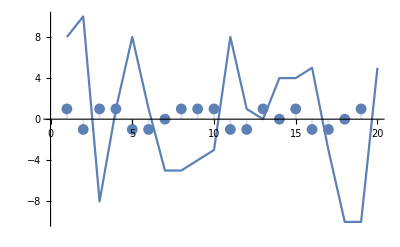

```mathematica
shape[v_] := Map[(Sign[#[[2]]-#[[1]]])&, Partition[v,2,1]];
values = RandomInteger[{-10,10},20]
Show[ListLinePlot[values],With[{s=shape[values]},DiscretePlot[s[[i]], {i, 1, 19}]] ]
```

Under Java, these problems are intended to be solved with a single for-loop that maintains some kind of state information that allows it to determine if there has been a violation in the requirement for the shape. In Mathematica, we aim for a more functional approach. The first question is just a simple counting question to get the students started with these definitions, asking to compute the number of positions in the array that are upsteps.

```mathematica
countUpsteps[v_] := Count[shape[v], 1];
countUpsteps[values]
```

9

The second question asks the method to determine whether two arrays of same length have the exact same shape. The short solution with Mathematica can be quite slow since it calculates the entire shape for both lists even when the first two elements would already determine that the answer is False. This seems a bit silly when these lists contain a million elements each, so perhaps we shall here grant a point for the imperative approach. After all, there is probably some good reason why real programmers don’t use pure functional programming for everything and, as the famous quip points out, nobody had yet to write an operating system kernel in a functional programming language. (As discussed in the late excellent blog “Programming in the 21st Century”, even writing a simple real time arcade game such as Pacman or Space Invaders, a task that a bunch of longhair potheads somehow managed to finish and ship on an industrial scale back in the seventies using programming environments that would make today’s programmers run home crying for mommy, is surprisingly difficult to do using the finest pure functional programming languages of our time. So something is clearly wrong with this entire big picture, although it is hard to put in words exactly what that something could be.)

```mathematica
sameStepShape[v1_,v2_] := shape[v1] == shape[v2];
```

The third question is a bit more interesting in that it asks for a method that can determine whether the shape of its parameter array is a sawtooth so that the array contains no plateaus, and every upstep is immediately followed by a downstep and vice versa. The absolute magnitudes of these upsteps and downsteps do not matter, only the fact that the forward differences need to alternate with respect to their signs. The first step can be either an upstep or a downstep, and the method has to work correctly for either one. The intended Java solution might look something like the following, if it were “transpreted” (to coin a term) directly to Mathematica. The local variable prev remembers the direction of the step in the previous position, and if the current step curr is ever equal to prev, we have found a violation of the definition of the sawtooth shape and can terminate the function right away without looking at the rest of the elements. (Beginning students sometimes find it difficult to understand that if the method verifies an universal claim, it can stop and return false at the first counterexample and ignore the rest of the elements, but that method cannot return true until it has looked at the entire array. Such seemingly obvious things are not always that obvious to beginners, especially if they also happen to feel that every if-statement must also include an else that does something.)

```mathematica
isSawtoothLoop[v_] := Module[{i, isGood = True, prev = 0, curr},
For[i = 1, i < Length[v], i++,
curr = Sign[v[[i+1]] - v[[i]]];
If[curr == 0 || curr == prev, isGood = False; Break];
prev = curr;
];
isGood
];
isSawtoothLoop[{-1, 10, 7, 9, -2, 0, -2}]
```

True

One possible one-liner solution more in tune of the logical and functional spirit of Mathematica springs from the realization that the given list is a sawtooth if that list itself contains no plateaus, but then also the shape of its shape contains no plateaus since those would reveal that the original list had two consecutive steps of the same sign in those positions. Of course, the downside of the following solution is that it computes the entire shape array (and then its second-order shape array) even if the answer were already determined by the first couple of elements. This approach would therefore work much better in Python 3 and its lazy iterators that never produce any more elements than those actually needed to entail the result.

```mathematica
isSawtooth[v_] :=With[{s = shape[v]},And[Not[MemberQ[s, 0]], Not[MemberQ[shape[s],0]]]];
isSawtooth[{-1, 10, 7, 9, -2, 0, -2, -9}]
```

False

The last question turned out to be interesting over the years in that many students find it surprisingly difficult, but as the hint to this question says, this whole question really should be one straightforward loop through the array. This question asks for a method that determines whether the given array is a mountain so that its shape first goes up some number of steps (where the word “some” again means zero or more, to emphasize the essential truth that zero is always a possibility in programming that the logic of your code needs to be prepared for) and then goes down some number of steps (again allowing the same possibility of zero). The hint asks you to encode the rule “One you have gone down, you may not go up again” into an intended Java solution that might translate to Mathematica as the following module.

```mathematica
isMountainLoop[v_] := Module[{i, step, isGood = True, goneDown = False},
For[i = 1, i < Length[v], i++,
step = Sign[v[[i+1]] - v[[i]]];
If[step == 0 || (step == 1 && goneDown),  isGood = False; Break];
If[step == -1, goneDown = True];
];
isGood
];
```

The one-liner solution in Mathematica looks for a position that is a downstep followed by an upstep, thus by its existence contradicting the requirement that the list is a mountain.

```mathematica
isMountain[v_] := With[{s = shape[v]}, And[Not[MemberQ[s,0]],Not[MemberQ[Partition[s, 2,1], {-1, 1}]]]];
```

To convince ourselves that the previous two functions that test whether the list is a mountain are equivalent, we can run both functions over a ten thousand randomly generated lists of integers to verify that both functions produce the same answer for all these lists. This operation can also be implemented as a one-liner that generates a list of results of the equality comparisons between the results that the functions returned for the same randomly generated list, and then turns this list of truth values into a logical conjunction by using Apply (here abbreviated as @@ as is the usual way) to replace its head with And to quickly determine whether every part of that conjunction is True.

```mathematica
And @@ Table[
With[{v = RandomInteger[{-10,10},RandomInteger[{1, 20}]]},
isMountainLoop[v] == isMountain[v]
],{i, 1, 10000}]
```

True

## Lab Seven: Two-dimensional arrays

Having received enough theory and practice for how to think about one-dimensional arrays and how they are processed by looping through their elements one step at the time, the seventh lab of this course expands this thinking into the second dimension, which then should naturally generalize to arbitrary higher dimensions among the denizens of the human Flatland. After all, as the famous zero-one-infinity principle that the author also loves to point out to his students whenever he spots it somewhere puts it; allowing none is fine, and allowing just one is also fine, but once you allow there to be two of something, you must then allow any number of that something.
The key to writing Java code that works on higher-dimensional arrays is the plain realization that Java really only has scalars and one-dimensional arrays in the core language. What looks like, acts like and quacks like a two-dimensional array is in reality a one-dimensional array whose elements just also happen to be one-dimensional arrays. This flash of realization explains why it is a perfectly legal and meaningful operation to index a two-dimensional array using only one index; why the length of the two-dimensional array gives its number of rows; why the two-dimensional array can be ragged so that its rows have different lengths; and why an entire row of a two-dimensional array can be reassigned or swapped in O(1) time. The same principle also happens to be how Mathematica works, so that its n-dimensional tensors are really just linear lists whose elements are n - 1 dimensional tensors, and can be treated and processed just like any other list. (Due to the lack of strong expliclt typing during the compile time, the elements of Mathematica tensors do not all need to have the same dimension.)
The first question asks for a method to create the transpose of the two-dimensional array whose each row is guaranteed to have the same number of elements for this operation to be meaningful. This, of course, is just the Mathematica built-in function Transpose, so there is little point in giving this function a new name of our own. The second question of this week’s lab is more interesting, as it asks for a method that generates a one-dimensional array that contains the row minimums of the argument two-dimensional array. To again emphasize the idea that zero is always a possibility in programming that the logic of your code needs to be able to tolerate and handle without crashing, the method is expected to work even if some row has zero elements. The method specification defines the row minimum to be zero in that case. (In retrospect, the positive infinity would have been a more appropriate value for the minimum of an empty row.)

```mathematica
rowMin[{}] := 0;
rowMin[list_] := Min[list];
minValues[a_] := Map[rowMin, a];
minValues[{{-2,9, 42, -17}, {}, {5, 2, -4, 9}}]
```

{-17,0,-4}

The third question asks for a method that creates and returns a new two-dimensional array that has the given number of rows and columns, its elements consisting of the numbers from start counting upwards placed in the rows of this array but so that in every other row, these numbers are placed right to left instead of left to right. This matrix is easy to construct by partitioning the one-dimensional list of the required elements into the desired rows, followed by using MapIndexed to reverse the sublists located in even-numbered rows, here again using Mathematica one-based counting.

```mathematica
zigzagOrder[list_, idx_] := If[Mod[First[idx], 2]==1, list, Reverse[list]];
zigzag[rows_, cols_, start_] := MapIndexed[zigzagOrder, Partition[Range[start, start + rows * cols], cols]];
zigzag[6, 12, 10] // MatrixForm
```

(10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21
33 | 32 | 31 | 30 | 29 | 28 | 27 | 26 | 25 | 24 | 23 | 22
34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45
57 | 56 | 55 | 54 | 53 | 52 | 51 | 50 | 49 | 48 | 47 | 46
58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69
81 | 80 | 79 | 78 | 77 | 76 | 75 | 74 | 73 | 72 | 71 | 70)

The last question of this week treats the rows of the two-dimensional array as coordinates of points located in three-dimensional Cartesian space, so the question comes with a guarantee that every row of the parameter array contains exactly three elements, for the question to make sense to begin with. The required task is to find an antipodal pair of points whose distance from each other is as large as possible, and return that distance. This question would be an interesting exercise for a course in combinatorial geometry, but here in the first regular programming course instead of fancy programming course, we are content with the quadratic time all-pairs brute force solution. Since Subsets is a handy way to generate the list of all possible pairs, triples and higher-uples of elements, this entire function can again be written as a one-liner, followed by another line to handle the corner cases of a singleton set or or an empty set. In Mathematica, the same function can handle points in arbitrary dimensions. The distance metric also does not need to be hardcoded into the function, but the next example shows how to write a Mathematica function to take optional arguments that, since the language makes no distinction between symbolic expressions that are code and data, can themselves be functions.

```mathematica
maximumDistance[pts_List /; Length[pts] > 1, df_: EuclideanDistance] :=Max[Map[df[#[[1]],#[[2]]]&, Subsets[pts, {2}]]];
maximumDistance[pts_List, df_: EuclideanDistance] := 0;
```

Just to do something interesting with this problem, let us compute the average maximum distance within the set of uniformly chosen random points inside the unit rectangle, as a function of the number of points in the set. As n increases, this ought to converge to the diameter of the unit rectangle, which is the square root of two.

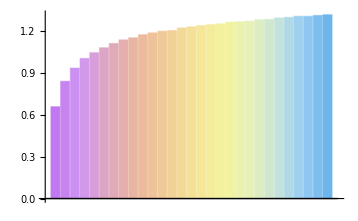

```mathematica
distanceSample[n_] := maximumDistance[RandomReal[{0,1},{n,3}]];
distanceTrial[n_, trials_] := Mean[Table[distanceSample[n], {trials}]];
BarChart[Table[distanceTrial[i, 1000], {i, 2, 30}], ChartStyle -> "Pastel"]
```

## Lab Eight: Recursion

In the author’s humble view, most of the introductory programming courses that he has seen teach recursion in a pretty wrongheaded way that is obviously meant to be taken by silent agreement between the teachers and students to be a forced formality that, in spirit, is probably really not that different from how the present day Chinese university students all still have to study the formally approved theory of Communism, just because that is the way that it is. The students leave the course with a misguided notion that recursion is basically a needlessly convoluted way to solve factorials and Fibonacci numbers and other similarly simple linear tasks that any sane programmer, assuming that he would even waste his working hours with such toy problems anyway to begin with, would instinctively solve with a simple for-loop to avoid a stack overflow and, in the case of a branching recursion that has repeated subproblems such as Fibonacci numbers, avoid the exponential blowup of running time during repeatedly solving the same small set of repeated subproblems all the way down.
Taking a little sidebar to the second course of algorithms, we recall that recursions that become exponential with repeated subproblems can usually be memoized to prevent these repeated subproblems to be recomputed from scratch each time, which given this author again a convenient excuse to emphasize the importance of the time-space tradeoff in all of computation when memory that would otherwise just be sitting idle is used to cache the results of computations that will be needed again in near future. Memoization is quite trivial to implement in Mathematica with the canonical pattern of lazy assignment of eager assignments. This memoized version of Fibonacci is, as they used to say back in the day, nearly “too cheap to meter” especially when compared to the exponential time version. (For a deep Fibonacci recursion, you still need to increase the value of the global variable $RecursionLimit to ensure that the evaluation does not crash with a stack overflow.)

```mathematica
fib[n_ /; n < 2] := 1;
fib[n_ /; n ≥ 2] := fib[n-1] + fib[n-2];
memFib[n_ /; n < 2] := 1;
memFib[n_ /; n ≥ 2] := memFib[n] = memFib[n-1] + memFib[n-2];
{First[Timing[fib[30]]], First[Timing[memFib[30]]]}
```

{4.20099,0.00019}

During the second half of the author’s introductory programming course, one entire three-hour lecture is used to go through the theory of recursion, up to and including memoization and why tail calls are better than ordinary recursive calls. This theory is then driven in with a dozen examples in the lecture and six more in this week’s lab, followed by the CodingBat sections on recursion to ensure that the students will really be able do that one recursion problem out of the four problems in their final exam. To avoid the simplistic view of recursion being a silly way to write a for-loop and instead bring out the power of recursion as a useful programming technique, the recursion lecture needs to offer interesting examples in which each recursive call branches to two more or recursive calls, which makes these functions not that straightforward to simulate with result-equivalent loops and nested loops, at least until the students become familar with the power of the deceptively simple data structure of a stack.
The author is therefore on a continuous hunt of simple but meaningful example problems that are best solved with branching recursion, such as opening all the safe tiles that emanate from the given zero-value tile in Minesweeper, or the subset sum problem to determine whether the given array of integers contains a subset whose elements exactly add up to the given goal. Discussion of the subset sum problem also allows pointing out the curious asymmetry of how very easy it is to verify whether the subset of integers that some guy offers to you adds up to the goal, and yet it is so strangely difficult to find a subset that works as a solution, despite the fact this Mickey Mouse problem consists of nothing but positive integers and their addition, and would be easy enough even for a ten year old to understand and solve by hand, at least in small instances. It is almost as if the computational reality and its “abstract physics” had an entirely different concept of “simple” than we humanoids.
Since Java does not have any easy and efficient way to extract a subarray from an array as a separate object (the low level C programming language turns out to out much better in this respect), all these array recursions are always written so that the same entire array object is always passed as argument at every level of recursion. The recursive method then receives additional indexing parameters that instruct that method to behave as if only that subarray had actually been passed to it, and ignore the rest of that array object entirely. The end result is just a good as if only the subarray had been passed in the recursive call.
Instead of writing the following solutions that way in Mathematica, these array problems actually make better examples of recursive pattern matching rules. The first of the six questions this week (the grading works this week so that points only start to accumulate from the third solved problem onwards, so that this lab gives the same two points as the other labs) asks for a recursive function to determine whether all elements of the array are equal. The following recursive rules say as base cases that all elements of an empty array and a singleton array are equal, and otherwise all the elements in the array are equal if the first two are equal and then all elements are equal from the second element onwards. The Mathematica pattern of a single underscore matches any single expression, the pattern of two underscores matches any sequence of one or more expressions, and the pattern of three underscores matches any sequence of zero or more expressions.

```mathematica
allEqual[{}] := True;
allEqual[{x_}] := True;
allEqual[{x_, x_, rest___}] := allEqual[{x, rest}];
allEqual[___] := False;
```

Mathematica is not Prolog so that it would automatically backtracking over rules. Instead, whenever you define multiple rules for the same symbol, only the first one that matches the argument pattern is actually used, similar to the behaviour of the if-else ladders of traditional imperative languages. Mathematica can and will usually internally rearrange the rules from the most specific to most general to resolve situations where the argument patterns overlap. In the previous example, the last rule that can match any sequence of expressions is the most general of these rules, but the other three preceding rules are disjoint in the sense that no argument pattern can match more than one of them at the time. Unlike in Prolog, where the query fails unless a solution is found during backtracking, in Mathematica the default result of failure (that is, default in the sense of the closed world assumption implicit in Prolog) has to be explicitly encoded as a kind of “none of the above” rule. This last rule then allows us to write queries such as allEqual[2 + foo] that are legal expressions but whose result we define to evaluate to False.
The second question of this week asks the student to implement System.arraycopy using recursion. Since mutating assignments over arrays go deeply against the functional spirit of Mathematica, we will now have to plead the fifth and politely decline to implement this function at all. (If really needed, the result list can always be trivially built up as a one-liner using Join and Take.) Instead, we shall move on to the third question that asks the student to implement the basic linear search algorithm using only recursion.

```mathematica
linearSearch[_, {}] := False;
linearSearch[x_, {x_, rest___}]:= True;
linearSearch[x_, {y_, rest___}] := linearSearch[x, rest];
linearSearch[___, ___] := False;
```

The fourth question continues in the same vein, asking the student to recursively reverse the order of the elements inside the given list.

```mathematica
reverse[{}] := {};
reverse[{x_}] := {x};
reverse[{x_, rest___}] :=Append[reverse[{rest}], x];
```

According to the student feedback, the fifth question this week is the most interesting and the most fun question of the entire slew of 42 questions in these ten labs. This question asks to implement the classic array partition algorithm that these students will then meet next year in the quicksort lecture of the normal introduction to algorithms course. Using the parity of the element as the partitioning criterion instead of comparing it to the pivot element, tthe elements of the given list of integers are to be rearranged so that all odd elements come first as one clump, followed by all even elements as another clump. This abstract problem is, of course, agnostic to the actual criterion used to separate the elements, and the basic logic of the function could be written to be the same and work with any possible criterion.
To have some variety for these recursion problems, we wll solve this particular problem using an additional accumulator parameter (in the following code named stack) that is used to gather the even numbers that happened to be encountered along the way during the recursion. In this programming style, the top level call first always calls to the accumulator version of the same function. The base case of the recursion is rewritten to return the value of the accumulator parameter instead of what would have been the ordinary answer for the base case. The recursive rules place the current element x either into the answer or into to stack depending on whether the element x is odd or even, that is, which side of the partitioning criterions it happens to fall on. Note also how the use of the accumulator parameter turns each rule tail recursive so that no other computation takes place after the recursive call. This allows the execution environment to recycle the current stack frame of recursion and avoid the possibility of stack overflow, which is why the accumulator parameter technique can be quite useful in traditional imperative programming languages.

```mathematica
parityPartition[x_] := parityPartition[x, {}];
parityPartition[{}, stack_] := stack;
parityPartition[{x_ /; Mod[x, 2] != 0, rest___}, stack_] := Join[{x}, parityPartition[{rest}, stack]];
parityPartition[{x_ /; Mod[x,2] == 0, rest___}, stack_]:= parityPartition[{rest},Append[stack, x]]; 
parityPartition[{4,-2,7, 1, 9, 0}]
```

{7,1,9,4,-2,0}

As a quick aside, it is also good to be aware of how the integer remainder operator works, should your logic potentially require computing the parities of negative elements. The sign of the remainder is always the same as the sign of the first operand, so that the sign of the second operand does not matter. This is the only mathematically meaningful way to define the remainder so that the quotient and remainder satisfy the equation binding them to the original operands of the integer division.

```mathematica
Map[Mod[#[[1]], #[[2]]]&, {{7,2},{-7,2},{7,-2}, {-7,-2}}] 
Map[QuotientRemainder[#[[1]], #[[2]]][[2]]&, {{7,2},{-7,2},{7,-2}, {-7,-2}}]
```

{1,1,-1,-1}

{1,1,-1,-1}

The last question is an example problem seen in the lectures a couple of weeks earlier, but this time this very problem must be solved using recursion instead of the straightforward for-loop through the positions. The problem ask to count how many runs of equal consecutive elements there exist inside the given list, with each singleton element being a trivial run of length one. This question is equivalent to counting how many elements inside the list are not equal to the next element, with the boundary condition that the last element of the list is considered to be different from the nonexistent element after it.

```mathematica
countRuns[{}] := 0
countRuns[{x_}] := 1;
countRuns[{x_, y_, rest___}] := If[x == y, 0, 1] + countRuns[{y, rest}];
```

## Lab Nine: Those dreaded word problems

The ninth lab of this course consists of four problems that each receive an ArrayList<String> of words as an argument, and these methods have to create and return another ArrayList<String> that contains precisely those words that match the requirement given in the problem specification. To test out these methods, a massive Unix wordlist of about 250,000 words of the English language is slurped into the JUnit tester. From this embarrassment of riches, only the proper words that consist of lowercase characters from a to z are kept in. This still leaves in about 210,000 words, most of which are technical terms of various fields of scientific and other endeavour so that the author estimates that, based on some random sampling done as a side effect of the Hangman programming project the author once used when teaching this course in the daytime mainline, he could reliably provide a definition for about one tenth of these words while standing on one foot. For the purposes of keeping this document self-contained, we shall instead use the built-in dictionary of Mathematica, since it still gives us more than enough words to play around with.
Implementing the Java solutions does not require any use of regular expressions, since such mythical beasts haven’t even been mentioned during this first programming course. Instead, all these methods are intended to be implemented by using ordinary loops through the characters of the individual words, with some comparisons then done inside the bodies of these loops. But with Mathematica, we are always allowed to use whichever particular blade of this giant Swiss army knife would best suit the task at hand. Since the author is more accustomed to regular expressions, the following solutions use them instead of the StringExpression objects of Mathematica. The same is presumably the case for most of the readers of this document. Our first regular expression matches precisely the words that contain only lowercase characters a to z from start of word to its end. The function RegularExpression can convert any regular expression into a Mathematica string pattern anyway, and even if you wanted to be explicit for purposes of readability and consistency, the official documentation offers handy tables of how these two symbolisms can simulate each other.

```mathematica
words = DictionaryLookup[RegularExpression["^[a-z]+$"]];
Length[words]
RandomSample[words, 20]
```

81288

{flightiness,thermoluminescence,followers,nonprofit,fantasying,sixteen,heritable,disorientates,myself,tobacconists,bottles,slowcoaches,pregnancy,delight,importance,largo,swings,traceries,defaces,intuitionistic}

In this week’s first lab problem we imagine that we are playing Hangman, and would like to find out which potential words are still theoretically possible based on the current pattern that emerged from our  previous hits and misses. (We assume that the parameter list contains only the words that the previous misses have not already eliminated.) The pattern is given as the characters that we have correctly guessed so far in their revealed positions. A question mark character is used as a character wildcard to denote those positions whose true characters are yet to be discovered. It is important to realize that unlike an ordinary pattern matching wildcard in regular expressions and elsewhere, a question mark can match only those characters that are not already part of the revealed pattern as they were successfully hit by the previous guesses. For example, the words “bridge” and “drudge” match the pattern “?r??ge”, whereas the words “dredge” and “grunge” do not. In the following solution, the Hangman pattern is converted into a regular expression where each question mark becomes the negated character class of all the letters that are already part of the pattern.

```mathematica
hangmanPattern[pat_] := With[{forbid = StringJoin["[^",Union[DeleteCases[Characters[pat], "?"]],"]"]},
RegularExpression[StringReplace[pat, "?" -> forbid]]
];
findMatchingWords[words_, pattern_] := With[{hp = hangmanPattern[pattern]},
Select[words, StringMatchQ[#, hp]&]
];
findMatchingWords[words, "?r??ge"]
```

{bridge,cringe,drudge,fridge,fringe,orange,triage,trudge}

The second question turns the standard palindrome identification programming exercise upside down, and asks the method to cherry pick all semordnilaps from the given list of words. A semordnilap (read it backwards) is humorously defined to be a word that produces a different legal word when it is read backwards. Since the Mathematica wordlist is given in sorted order (and even if it weren’t, one quick call to Sort would fix that), we can use binary search to quickly determine whether the reversed version of the given word is also a word. This one is again a point for Java, where that function is already implemented in the Collections utility class, but Mathematica seems to be oddly lacking this fundamental computer science algorithm. But that is just all the better for our purposes, since implementing binary search gives us a chance to practice writing modules and while-loops.

```mathematica
binarySearch[words_, w_] := Module[{i = 1, j = Length[words], mid},
While[i < j, 
mid = Floor[(i+j)/2];
If[Order[words[[mid]], w] == 1, i = mid + 1,  j = mid];
];
words[[i]] == w
];
findSemordnilaps[words_] := Select[words, (With[{rev = StringReverse[#]}, rev ≠ # && binarySearch[words, rev]])&];
findSemordnilaps[words]
```

{abut,agar,ah,am,animal,are,at,ate,auks,avid,bad,bag,ban,bard,bat,bats,bed,bin,bod,bog,bonk,boy,brag,bud,bun,buns,bur,burg,bus,but,buts,cam,cod,dab,dag,dam,dart,deb,debut,decaf,decal,deem,deep,deeps,deer,deffer,deliver,denier,denies,denim,deres,desserts,devil,dew,dial,dialer,diaper,dim,diva,dob,doc,dog,don,doom,door,dos,drab,draw,drawer,draws,dray,dual,dub,edit,eel,eh,em,emir,emit,er,era,ergo,eta,etas,evil,eviler,faced,fer,fires,flog,flow,gab,gad,gal,gals,gar,garb,gas,gel,gem,girt,gnat,gnus,gob,god,golf,got,grub,gulp,gulper,gum,gums,guns,gut,ha,hap,he,ho,hoop,it,jar,keel,keels,keep,knits,knob,know,laced,lag,lager,laid,lair,lamina,lap,laud,lee,leek,leer,leg,leper,lever,liar,lit,live,lived,loop,loops,loot,looter,loots,lop,ma,mac,macs,mad,maps,mar,mart,mat,maws,may,me,meed,meet,meg,mid,mils,mined,mood,moor,mop,mot,mu,mug,nab,nap,naps,net,new,nib,nip,nips,nit,no,nod,not,now,nub,nus,nut,nuts,ogre,oh,on,oohs,pacer,pah,pal,pals,pan,pans,par,part,parts,pas,pat,paws,pay,peed,peek,peels,pees,per,perts,pets,pin,pins,pis,pit,plug,pol,pols,pom,pooh,pool,pools,ports,pot,pots,prat,pus,rag,raga,rail,raj,ram,rap,raps,rat,rats,raw,re,rebut,recap,recaps,redraw,reed,reel,ref,reffed,regal,reined,relaid,relive,remit,rennet,rep,repaid,repel,replug,retool,retros,revel,reviled,reward,rial,rime,rood,room,rot,rub,sag,sap,saps,sate,saw,scam,seep,seined,sered,serif,shoo,sip,six,skua,slag,slap,sleek,sleep,sleets,slim,sloop,sloops,slop,smart,smug,smut,snap,snaps,snip,snips,snit,snoops,snot,snub,snug,sod,sorter,spacer,spam,span,spans,spar,spas,spat,spay,speed,spin,spins,spit,spool,spools,spoons,sports,spot,spots,sprat,stab,star,steels,step,stew,stink,stool,stop,stops,stows,strap,straw,strep,stressed,strop,strops,stub,stun,sub,sun,sung,sup,swam,swap,sward,sway,swot,swots,ta,tab,tam,tang,tap,taps,tar,tarp,tarps,teem,ten,tenner,ti,tide,til,time,timer,tin,tins,tip,tips,tog,tom,ton,tons,tool,top,tops,tor,tort,tow,tows,trad,tram,trams,trap,trig,trot,trow,tub,tuba,tubed,tuber,tug,tums,tun,um,war,ward,warder,warts,was,way,wed,wen,wets,wolf,won,wonk,wort,wot,xis,yam,yap,yaps,yard,yaw,yaws,yob}

Finding all anagrams of the given word is another boilerplate programming exercise for the second programming course of which this lab is giving a sneak preview. The intended solution of this problem, given as a hint to the students, is to sort the arrays of characters of the words and compare these arrays for equality to determine whether these two words are anagrams. (Alternatively, since in this problem there are known to be exactly 26 different characters, we could use an array of counters incremented elementwise by one for-loop through each word, and then compare the pairwise equality of the resulting counters.)
To make this problem more fun and Mathematica-l, we recall the Fundamental Theorem of Arithmetic that guarantees that every positive integer has a unique prime factorization. This theorem can be used to convert words to integers so that two words become the same integer if and only if they are anagrams. Each of the 26 lowercase characters that can appear inside a word is mapped to a prime number, after which the Gödel number of each word is the product of the prime numbers that encode the characters in the word. Since integer multiplication is orderless, two anagrams must necessarily produce the same Gödel number, so we can effectively use this Gödel number as a hash code that is consistent with respect to the equivalence relation of anagrams. The function Thread is a handy way to “zip” two lists of same length together into one list whose each element is a pair of corresponding elements of the original lists, combined together under the given head. The list of substitution rules produced this way is used to convert the extracted letters of the word into the list their corresponding prime numbers, which are then multiplied together simply by applying Times to the head of this list. Mathematica is not needlessly picky about what characters it accepts in function names.

```mathematica
primeEncode = Thread[(#1 -> #2)&[CharacterRange["a", "z"],Table[Prime[i], {i, 1, 26}]]]
gödelNumber[word_] := Times @@ (Characters[word] /. primeEncode);
gödelNumber["hello"]
gödelNumber["supercalifragilisticexpialidocious"]
```

{a→2,b→3,c→5,d→7,e→11,f→13,g→17,h→19,i→23,j→29,k→31,l→37,m→41,n→43,o→47,p→53,q→59,r→61,s→67,t→71,u→73,v→79,w→83,x→89,y→97,z→101}

13447687

7549206708138164397666367808363985304525621000

The anagrams of the given word can now be identified by the equality of their Gödel numbers. To speed up the computation, we use the length equality comparison as a quick rejection test before computing the Gödel number that bears the real brunt of this comparison.

```mathematica
findAnagrams[words_, w_] := With[{g = gödelNumber[w]}, Select[words, (Length[#] == Length[w] && gödelNumber[#] == g)&]];
findAnagrams[words, "pastel"]
```

{palest,pastel,petals,plates,pleats,staple}

The fourth question of this penultimate lab, a new one for the current semester whose completion inspired the author to write this document, turned out to be just too difficult for students, so it was left out of the marking of the lab altogether. Regular expressions would make short work of this problem, but without that formalism, the working recursive solution is not really that obvious, and the loop solution that the instructor had in mind actually turned not to work when implemented as simply as was originally planned.
The problem specification is otherwise the same as the first problem of wildcard matching, but now the wildcards are asterisks that can match any sequence of zero or more characters that are now allowed to be any characters, including those that occur somewhere else in the pattern. (Would it be possible to create a version of Hangman where each guess could be some more general pattern than merely a single letter? That little aside might be a topic to explore in a different day.) We can try out this implementation by using it to find out how many words in English contain the letter a exactly four times.

```mathematica
starPattern[pat_] := RegularExpression[StringJoin[Characters[pat] /. "*" -> "(.*)"]];
findMatchingWordsStar[words_, pattern_] := With[{sp = starPattern[pattern]},
Select[words, StringMatchQ[#, sp]&]
];
Complement[findMatchingWordsStar[words, "*a*a*a*a*"], findMatchingWordsStar[words, "*a*a*a*a*a*"]]
```

{adiabatically,amalgamate,amalgamated,amalgamates,amalgamating,amalgamation,amalgamations,ambassadorial,anagrammatic,antimacassar,antimacassars,antimalarial,baccalaureate,baccalaureates,bacchanalia,bacchanalian,bacchanalians,balaclava,balaclavas,balalaika,balalaikas,caravansaries,caravansary,catamaran,catamarans,diagrammatically,extravaganza,extravaganzas,jacaranda,jacarandas,jambalaya,lackadaisical,lackadaisically,macadamia,macadamias,maharajah,maharajahs,palatalization,paradisaical,paraphernalia,parliamentarian,parliamentarians,phantasmagoria,phantasmagorias,phantasmagorical,sarsaparilla,sarsaparillas,tarmacadam,whatchamacallit,whatchamacallits}

## Lab Ten: The Endgame

As the grande finale for the students who have spread their wings and flown out of their nest, no longer helpless little hatchlings for whose tiny beaks and stomachs everything must be carefully regurgitated, but who have become mighty fearsome eagles that sink their newfound programming talons into any problem placed in front of them, this last lab serves a buffet of generalized chess problems for an arbitrary n-by-n board, just so that these students can practice their two-dimensional thinking a little bit more. Same as with the card games in the second and third labs, no knowledge of the game of chess itself is necessary to solve these problems. On the other hand, considering the social and cultural importance of the game of chess in all cultures in East and West, the basic moves of the different types of chess pieces should be elementary common knowledge of all educated adults anyway, so if they are not, it is high time to learn them now.
Since the algorithm theory lecture two weeks before this lab strongly emphasized the importance of not being “Shlemiel the Painter”, as named by Joel Spolsky in his Internet-famous blog post decades after Jon Bentley’s books on code optimization had long delved on that particular type of code optimization problem, these problems are strongly emphasized not use more nested loops than are necessary. Again, the JUnit tester class for this week’s lab is intentionally designed to be hard and heavy enough so that any Shlemiel solutions will take painfully long to execute, whereas tighter solutions can finish the job in a fraction of second. The threshold between linear time versus quadratic time algorithms is the surely most important algorithmic issue in everyday practical programming. It is pretty rare for most working programmers to do something that requires potentially exponential combinatorics, but every programmer writes linear for-loops and nested for-loops on a daily basis.
Of course, the higher-level the language is and therefore covers up the details of the true computation of zeros and ones that take place underneath the layers of abstractions of the language that are just as made-up and fictional as hobbits and vampires (but still as functional for the purposes of expressing higher level ideas), the more difficult it is for the programmer to reason about the actual wall clock running time of various possible implementations, as the C programmers will never tire pointing out. Working on problems suited for Mathematica we pretty much ignore all small efficiencies anyway and concentrate on just solving the problem itself. The minutes and potentially more saved by solving the problem as a one-liner will then more than compensate for the execution time being some split second longer.
The first question starts off by asking for a method that counts how many squares in the n-by-n chessboard are safe from the all chess rooks that have already been placed somewhere on the board. The parameter board is guaranteed to be an n-by-n matrix of truth values whose elements are True for a square that contains a rook, and False for an empty square. Using the observation that a row or a column is unsafe if any one of its squares contains a rook, this unsafety can be expressed as a logical disjunction between the elements of that row or column. Since permuting the rows and columns does not change the answer to this question, we can imagine all the safe rows and safe columns to have been permuted to be together in one clump, making that answer to be the product of these counts of safe rows and safe columns free of threatening rooks and other mooks.

```mathematica
countSafeSquaresRooks[board_] :=With[{unsafeRows = Apply[Or, board, {1}], unsafeCols = Apply[Or, Transpose[board], {1}]},
Count[unsafeRows, False] * Count[unsafeCols, False]
];
```

The second question gives the method a board that contains chess knights of the same colour placed on that board, and asks for the count of how many different possible moves exist in that situation. Each chess knight can move up to eight other squares, jumping over another chess knight if necessary, but it cannot move outside the board or into a square that is already occupied by another chess knight of the same colour. As a hint to get started with this problem, the lab specification provides an array of possible move offsets that describe the possible moves of a chess knight, relative to its present position.

```mathematica
knightMoves = {{2,1},{1,2},{-1,2},{-2,1},{-2,-1},{-1,-2},{1,-2},{2,-1}};
```

The total number of moves on this board is then the sum of the counts for possible moves for each individual knight. So that the entire board does not get copied every time we compute the number of moves in the given square, this function is written as a Module whose inner functions then all see and share the same board.

```mathematica
countKnightMoves[board_] := Module[{n = Length[board],inside,moves},
inside[row_,col_]:= 1 ≤ row ≤ n && 1 ≤  col ≤ n;
moves[row_,col_] := If[board[[row,col]], 
Count[Table[With[{nr = row + m[[1]], nc = col + m[[2]]},inside[nr,nc] && Not[board[[nr,nc]]]], {m, knightMoves}], True]
,
0];
Total[Table[moves[row,col],{row,1,n},{col,1,n}], 2]
];
```

The third question is similarly counting the number of possible moves on the argument board, but now for the first time for this lab, this calculation is performed for a board that contains some number of both black and white pieces. In this question, each piece is a pawn of either colour. As per the rules of chess, a chess pawn can move one step forward to an empty square, or capture forward-left or forward-right another pawn of the opposite colour. (For simplicity, we ignore the pawn promotions in the last row, and also the en passant capturing moves that would require additional bits of state information to remember how a pawn got to the square that it is currently in.) The parameter board is now a matrix of individual letter characters so that w represents a white pawn, b represents a black pawn, and the whitespace character represents an empty tile.
As always in these labs, the problem guarantees that these are the only possible characters that can occur on the given board, and the the board is guaranteed to be a square of dimensions n-by-n for some n, so that the method does not need to perform error handling for illegal argument values. The method specification recommends not to copy-paste and duplicate the essentially same block of code separately for white and black pawns, but the same block of code logic, if parameterized accordingly, could correctly handle both colours. As the author loves to emphasize in all his courses whenever he can, whenever you copy-paste your own code within the same project, that is a code smell that guarantees that you are doing something wrong for sure. Even if the code happens to work for now, it is needlessly complex and will easily fail when modified in the future.

```mathematica
countPawnMoves[board_] := Module[{n = Length[board], inside, moves, forward},
inside[row_,col_]:= 1 ≤ row ≤ n && 1 ≤ col ≤ n;
forward[row_, piece_] := If[piece == "w", row-1, row+1];
moves[row_,col_] := If[board[[row,col]] == " ", 0,
With[{piece = board[[row,col]]},
With[{oppo = If[piece == "w", "b", "w"], r2 = forward[row, piece]},
If[inside[r2,col] && board[[r2,col]] == " ", 1, 0] +
If[inside[r2,col-1] && board[[r2,col-1]] == oppo, 1, 0] +
If[inside[r2,col+1] && board[[r2,col+1]] == oppo, 1, 0]
]
]];
Total[Table[moves[x,y],{x,1,n},{y,1,n}], 2]
];
```

The final question of all these labs is otherwise the same as the first question of this lab, but this time done for the chess queens instead of rooks. The ability of queens to move diagonally makes the computation of threatened squares more complicated than it was for the more well-behaved rooks that threaten only the same column and the same row that they are in. Fortunately, another quick googling reveals that the matrix operations of Mathematica happen to include the function Diagonal to extract the given diagonal of the matrix so that the diagonal 0 is the main diagonal, and positive numbers denote the diagonals above them.

```mathematica
countSafeSquaresQueens[board_] := Module[{n = Length[board],upsideDown = Map[Reverse, board],unsafeRows, unsafeCols, unsafeSE, unsafeSW, safety},
unsafeRows = Apply[Or, board, {1}];
unsafeCols = Apply[Or, Transpose[board], {1}];
unsafeSE = Table[Apply[Or, Diagonal[board,k]],{k, -n+1, n-1}];
unsafeSW = Table[Apply[Or, Diagonal[upsideDown,k]],{k, -n+1, n-1}];
safety[row_,col_] := If[unsafeRows[[row]] || unsafeCols[[col]] || unsafeSE[[n - row + col]] || unsafeSW[[2*n+1-row-col]], 0, 1];
Total[Table[safety[row,col], {row, 1, n}, {col, 1, n}], 2]
];
```

## Conclusions

The private model answers of these ten labs prepared by the instructor, to prove that the lab is feasible and that the shared JUnit testers would have known checksums to compare the student submissions to, together contain 670 lines of code. Discounting for the curly braces and other similar waste of vertical space, this would roughly translate to about 500 lines of actual meaty goodness of code. The above solutions written in Mathematica do not contain even close to that many lines, even if we included all those lines that are for demonstration or sanity checks, or that perform all that extra stuff that was spun out of these lab problems. (Without bothering to actually count, the author offers a rough Stetson estimate of 100 lines, for an average of about 2.5 lines per problem.)
Of course, everyone has to admit that compiled imperative languages still have a massive advantage when it comes to actual execution speed. At this writing, using the author’s trusty six year old Mac desktop, it takes about two and a half minutes to ecaluate all of the expressions in this notebook starting from fresh kernel. But the execution time of a complicated function really matters only if the function is to be executed many times by many people, otherwise the time spent thinking and coding the function is the lion’s share of the total time.
We leave it as exercise for the reader to rewrite any of the previous lab solution functions to run more efficiently, noting how the Timing function in Mathematica then makes it very easy to measure the execution times of arbitrary computations. An interestered reader operating on any modern-day multicore machine can also try out the speedup effects of using ParallelTable in place of Table, or the more general function Parallelize that, in the finest spirit of Mathematica and the complete representational equivalence of code and data, uses Mathematica itself to evaluate the clever pattern matching rules that determine the best way to parallelize the execution of some high-level expression tree. In functional programming, since code and functions are expression trees in no way different from what we normally think of as data, functions can be written to analyze and create other functions (and also, of course, themselves) just like they can analyze and create any other data.
Your humble narrator does not claim to be anything but an amateur enthusiast dabbling in Mathematica, so surely for all of these problems, those with more experience with this wonderfully concise and powerful language could have come up with solutions that are not just significantly more efficient, but also more elegant in their conformance to the spirit of functional programming. (The author would always be interested to see these solutions.)
But most importantly, especially after two decades of imperative programming, Mathematica is just way more fun than Java mired in all its bureaucratic verbosity. For example, at least until last week from this writing when Java 10 was released to finally allow the use of var in local variable declarations to mean the type of whatever is the formal type of the right hand side of the initialization, the Java language always required the programmer to say that 42 is an integer when assigning that value to a fresh new local variable, just to prove to the compiler that the programmer also knows the secret password to the treehouse and yes, he is also aware of the fact that 42 is an integer and can thus be relied to write his code correctly based on that assumption.
Constrast this to Mathematica, where the programmers can just say what they want done and let the pattern matching engine fill in the detais. In Java, having first written the method that computes the shape of a bridge hand, the extra effort required to write the code that tabulates all possible hand shapes according to their relative frequencies is just that, effort. Working in Mathematica, questions and ideas of that nature simply come out as casual little afterthoughts, and they can be implemented with a couple of lines of additional code.
Personally for the author, Mathematica has taught a newfound appreciation of the advantages of functional programming that he can still remember being unable to understand (or as the term was back then, to grok) at the beginning of his career when reading and hearing a couple of LISP enthusiasts hanging around tout the advantages of their style, when all you can see is Lots Of Silly Parentheses. But if you take the LISP lists and change all parentheses into square brackets, and move the first element to the syntactic position before the left square bracket, surely you are not changing anything essential. As you are also not changing anything if you follow the convention of capitalizing each name that is part of the standard library, or by using a graphical front end that shows the results of computations not as the deeply nested and hard to read expression trees that they really are, but as various graphical forms chosedn by the head of that expression. Add to this mix a high level pattern matching system that serves as intelligent runtime macros, and we suddenly realize that Mathematica makes the promises of LISP available in a form that Joe Average can readily understand and use. And these days, try out for free online on Wolfram Cloud.